## Lab 5 Francesco Vassalli

### Introduction

Op-amps can be used to create inverting, summing, and integrating circuits.  The summing amplifier is an elementary example of a digital analog converter (DAC).  The circuit can also be used to handle analog signal addition.  We create several circuits using the inverting op-amp set up to demonstrate the ability of basic inverting circuits, summing circuits, and integrators.  We also predict and measure key op-amp performance indicators and the frequency dependence of our inverting circuits.  We also measure the performance of a simple three bit DAC.  We demonstrate how the integrator responds to several input signals.

### Experiment

-Graphics-

Inverting op-amp circuit

G_0=-R_f/R

B=R/(R+R_f)

f_T=(-G_0 f_B)/(1-B)

G=G_0/(1+ⅉf/f_B)

```mathematica
Grid[{{"Key Value","Predicted","Measured"},{"G_0","10.09","11.43"},{"f_B","450.8kHz","450kHz"},{"f_T","5MHz","5.143MHz"}},Frame->All]
```

Key Value | Predicted | Measured
G_0 | 10.09 | 11.43
f_B | 450.8kHz | 450kHz
f_T | 5MHz | 5.143MHz

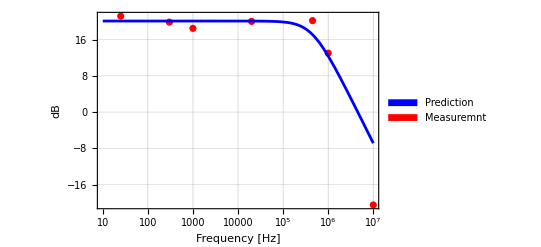

```mathematica
f={25,300,10^3,2*10^4,45*10^4,10^6,10^7};
dB[vout_,vin_]:=20*Log[10,vout/vin];
dBg[g_]:=20*Log[10,g];
A0=25*10^3;
R=9.86*10^3;
Rf=99.5*10^3;
B=R/(R+Rf);
G0=Abs[A0(1-B)/(1+A0*B)];
fb=450.805*10^3;
gp[f_]:=Abs[G0/(1+(ⅉ*f)/fb)];
predict=LogLinearPlot[dBg[gp[f]],{f,10,10^7},PlotRange->All,PlotStyle->{Blue,Thickness[.005]}];
vin={1.05,1.05,1.05,1.05,1.02,1.03,.76};
vout={12,10.3,8.8,10.5,10.4,4.6,.072};
measure= ListPlot[Thread[{f,Table[dB[Part[vout,i],Part[vin,i]],{i,1,Length[vin]}]}],
ScalingFunctions->{"Log"},
Frame->True,Axes->True,
LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"Frequency [Hz]","dB"},
FrameStyle->Thickness[.005],PlotStyle->{Red,Thickness[.01]},GridLines->Automatic,PlotLegends->SwatchLegend[{Blue,Red},{"Prediction","Measuremnt"}]];
Show[measure,predict,PlotRange->All]
```

Bode plot for the inverting circuit.

We use equations 1-4 to predict the behavior and key values for the depicted circuit.   The predicted values were calculated from the spreadsheet specifications. The frequency dependence agrees with the prediction, but there is disparity between the f_Tmeasurement and prediction due to disagreement in the G_0 measurement.  The simple op-amp model begins to fail at very high frequency we could refine by accounting for additional capacitance in the circuit.

Schematic for the summing amplifier.

V_out=-(V_1/R_1+V_2/R_2+V_3/R_3)R_F

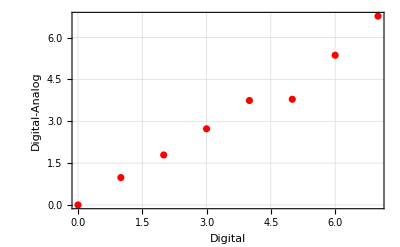

```mathematica
vout={6.772,5.370,3.79,3.745,2.731,1.793,.982,0};
p={7,6,5,4,3,2,1,0};
diffPlot=ListPlot[Thread[{p,vout}],
Frame->True,Axes->True,
LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"Digital","Digital-Analog"},
FrameStyle->Thickness[.005],PlotStyle->{Red,Thickness[.01]},GridLines->Automatic]
```

Input digital values to our DAC and record the analog output. This displays the residual.

We use the summing amplifier to create a DAC and vary the input voltages to simulate 3 bit input. The residuals demonstrate that there is good differentiation between the DAC’d values except at 4 and 5.

Schematic of our integrator circuit.

V_out(t)=1/RC(∫_0)^t V_in dt

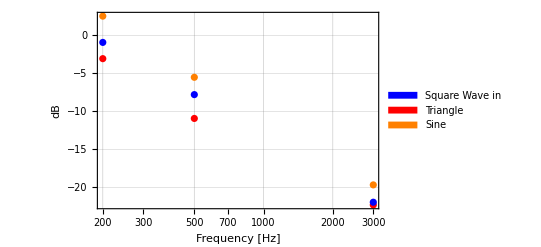

```mathematica
f={200,500,3000};
R=10^5;
cap=2.41*10^-6;
voutt={.760,.276,.076};
voutsq={.9,.4,.08};
voutsin={1.34,.520,.104};
vin={1.08,0.97,0.99,1,0.98,1,1.01,1,.99};
measure= ListPlot[Thread[{f,Table[dB[Part[voutt,i],Part[vin,i]],{i,1,3}]}],
ScalingFunctions->{"Log"},
Frame->True,Axes->True,
LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"Frequency [Hz]","dB"},
FrameStyle->Thickness[.005],PlotStyle->{Red,Thickness[.01]},GridLines->Automatic,PlotLegends->SwatchLegend[{Blue,Red,Orange},{"Square Wave in","Triangle","Sine"}]];
sqout=ListPlot[Thread[{f,Table[dB[Part[voutsq,i],Part[vin,i+3]],{i,1,3}]}],ScalingFunctions->{"Log"},PlotStyle->{Blue,Thickness[.01]}];
sinout=ListPlot[Thread[{f,Table[dB[Part[voutsin,i],Part[vin,i+3]],{i,1,3}]}],ScalingFunctions->{"Log"},PlotStyle->{Orange,Thickness[.01]}];
Show[measure,sqout,sinout,PlotRange->All]
```

This Bode plot shows the frequency dependence of our integrator circuit for square, triangle and square wave inputs.  Recorded is the Vpp gain once the output stabilized due to bleed.

Using equation 6 we predict that the output of the integrator circuit will have the function form of the integral of the input.  We did not predict the frequency dependence for the bleeding integrator circuit we could refine the model by calculating the attention once the voltage stabilizes. The integrator circuit is quick to attenuate which is not well described by equation 6.

### Conclusion

We used an inverting op amp to create a negative feedback circuit, summing amplifier, and integrator circuit.  The summing amplifier was used to make a 3-bit digital analog converter.  Finally we create an integrator circuit and verify that the output signal is the integral of the input.